# Diffusion constants for SE relation

### data loading

```mathematica
p0s={3.85,3.825,3.80,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 999999 ,999999}};
```

```mathematica
trueMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
trueCRMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueCRMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Normal[trueMSDs[[1,1,1,2]]]
```

{0.,7.76355×10^-6,0.0000310491,0.0000698444,0.000124131,0.000193884,0.000279071,0.000379655,0.000495592,0.00062683,0.000773314,0.000934977,0.00130355,0.0015103,0.00196826,0.00248486,0.00305922,0.00369036,0.00474122,0.00591348,0.00765766,0.00909525,0.0117227,0.0146188,0.0177597,0.0218196,0.0269079,0.0331179,0.0396799,0.048281,0.0581388,0.0692619,0.0826416,0.0973786,0.114614,0.135753,0.160024,0.187319,0.218171,0.252038,0.286479,0.323363,0.36222,0.404948,0.45344,0.510642,0.578552,0.65974,0.759284,0.862687,0.979511,1.11295,1.27804,1.46743,1.66922,1.8835,2.16433,2.47749,2.82554,3.24532,3.68043,4.17453,4.82108,5.55823,6.41966,7.30945,8.30295,9.44612,10.6483,11.8987,13.4339,15.1684,16.7585,18.7426,21.1581,23.7077,26.7083,29.6253,33.5696,37.481,42.6211,49.3029,57.2495,65.6917,75.514,88.2334,103.672,120.718,140.34,162.194,185.125,204.354,227.062,256.351,292.428,325.212,374.532,422.166,479.877,533.901,596.574,664.704,752.465,858.084,964.164,1067.51,1158.39,1261.06,1387.57,1513.06,1683.22}

### Mean MSD plot

Part::partw: Part 638 of … does not exist.

Part::partw: Part 639 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

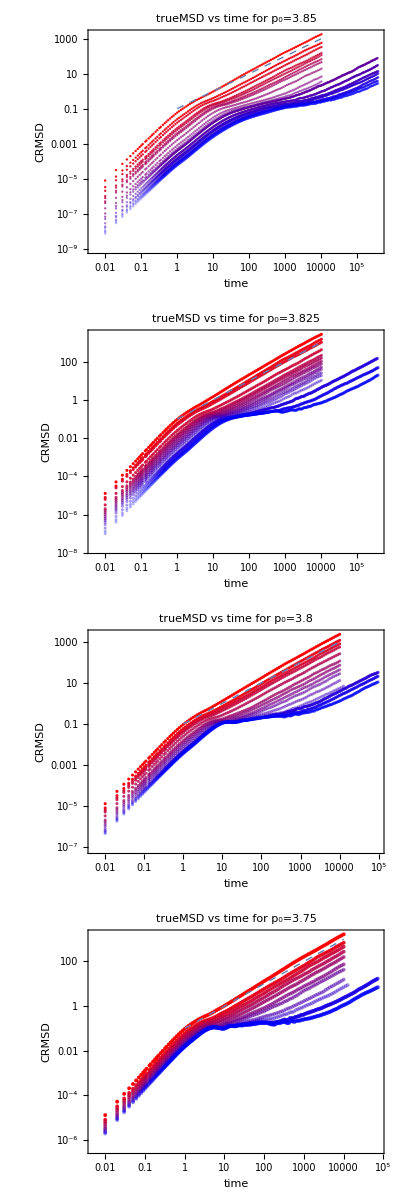

```mathematica
trueMSDMeanPlots=Table[Show[
ListLogLogPlot[Table[Table[{trueMSDs[[p,T,1,1,rec]]-trueMSDs[[p,T,1,1,1]],Mean[Table[trueMSDs[[p,T,i,2,rec]],{i,10}]]},{rec,Length[trueMSDs[[p,T,1,2]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRMSD"},ImageSize->600,PlotLabel->"trueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False],LogLogPlot[.1x,{x,1,10000},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[trueMSDMeanPlots]
```

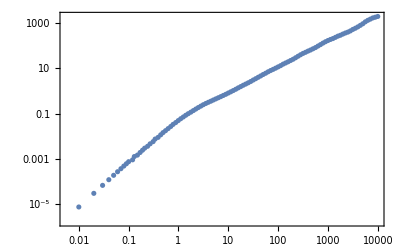

```mathematica
ListLogLogPlot[Table[{trueMSDs[[1,1,2,1,i+1]]-trueMSDs[[1,1,2,1,1]],trueMSDs[[1,1,2,2,i]]},{i,1,Length[trueMSDs[[1,1,2,1]]]-1}]]
```

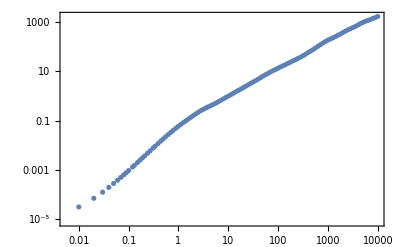

```mathematica
ListLogLogPlot[Table[{trueMSDs[[1,1,1,1,i]]-trueMSDs[[1,1,1,1,1]],trueMSDs[[1,1,1,2,i]]},{i,2,Length[trueMSDs[[1,1,1,1]]]}]]
```

## diffusion constants defined as lim_(t->inf) MSD/(4t)

### MSD

```mathematica
diffusionConstants=Table[Table[Table[trueMSDs[[p,T,i,2,Length[trueMSDs[[p,T,i,2]]]]]/4/(trueMSDs[[p,T,i,1,Length[trueMSDs[[p,T,i,1]]]]]-trueMSDs[[p,T,i,1,1]]),{i,10}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{0.0420804,0.0557526,0.0410715,0.0439529,0.0446329,0.0411676,0.0450024,0.042297,0.0443635,0.0441935},{0.0135362,0.0156349,0.0139247,0.0150584,0.0142123,0.0127187,0.0170498,0.0135849,0.0141933,0.013615},{0.00815028,0.0082435,0.00761923,0.0081441,0.00865473,0.00802436,0.00920181,0.00839252,0.0090655,0.00767415},{0.00364502,0.00402439,0.00322033,0.00364481,0.00450713,0.00390586,0.0038093,0.00363685,0.00370316,0.00359508},{0.00243385,0.00326056,0.00330465,0.00223807,0.00287952,0.00305018,0.00299049,0.0023479,0.00244938,0.0036887},{0.00189575,0.00204147,0.00137111,0.00193412,0.00151129,0.00144398,0.00184334,0.00159177,0.00166563,0.00146525},{0.00120896,0.00117582,0.00135036,0.00106751,0.000934697,0.00114519,0.00106171,0.00107043,0.00129801,0.000950025},{0.000496305,0.00042428,0.000653817,0.000389828,0.000444927,0.000436766,0.000553964,0.000494872,0.000461158,0.000446059},{0.000234432,0.00015508,0.000146685,0.000157138,0.000176687,0.000158683,0.000157599,0.000150398,0.000163881,0.000191646},{0.0000994477,0.0000902857,0.0000762656,0.0000927756,0.0000864471,0.0000669238,0.0000860934,0.000103203,0.000086303,0.0000946864},{0.0000568148,0.0000443763,0.000051782,0.0000529046,0.0000472788,0.0000770172,0.0000550647,0.0000486463,0.0000482657,0.00004865},{0.0000211042,0.0000216871,0.0000183649,0.0000214442,0.0000241889,0.0000204605,0.0000211348,0.0000196709,0.0000201541,0.000021167},{8.47025×10^-6,8.1392×10^-6,0.0000128839,8.63315×10^-6,8.42879×10^-6,0.0000101777,9.79878×10^-6,7.5014×10^-6,8.47011×10^-6,8.8961×10^-6},{6.49581×10^-6,7.89882×10^-6,6.1779×10^-6,6.4039×10^-6,6.05459×10^-6,8.00447×10^-6,6.04767×10^-6,7.70568×10^-6,6.75084×10^-6,6.64909×10^-6},{3.75097×10^-6,4.1198×10^-6,3.99182×10^-6,6.83524×10^-6,4.6103×10^-6,3.58277×10^-6,3.39378×10^-6,3.97167×10^-6,3.49269×10^-6,3.46812×10^-6},{2.53393×10^-6,2.28281×10^-6,2.69229×10^-6,3.71115×10^-6,2.03769×10^-6,2.49379×10^-6,2.79478×10^-6,3.01354×10^-6,2.64415×10^-6,2.31912×10^-6},{2.10518×10^-6,1.89731×10^-6,1.78719×10^-6,1.97768×10^-6,1.53716×10^-6,1.8437×10^-6,1.75054×10^-6,1.98256×10^-6,2.08378×10^-6,1.8283×10^-6}},{{0.067912,0.0717015,0.0654619,0.0653289,0.064024,0.067358,0.0677893,0.0680505,0.0638645,0.0670479},{0.0383987,0.0357471,0.034545,0.0358167,0.039369,0.0349823,0.0400543,0.0368407,0.036961,0.0356822},{0.0231207,0.0254737,0.0249167,0.0280677,0.0278681,0.0263851,0.0243296,0.0240546,0.0254212,0.0246653},{0.0106604,0.011084,0.0106962,0.0100877,0.00958186,0.0102189,0.01192,0.00964685,0.0102165,0.00976549},{0.0054864,0.0048201,0.00542159,0.005323,0.00576696,0.00502737,0.00478923,0.00443252,0.00513674,0.00640808},{0.00358879,0.00419419,0.00383455,0.00490496,0.00351981,0.00395184,0.00308989,0.00375375,0.00349183,0.00319534},{0.00247127,0.00265762,0.0025988,0.00238124,0.00269683,0.00275612,0.00251854,0.00238594,0.00255967,0.00279417},{0.00188789,0.00158753,0.0021264,0.00213394,0.0018041,0.00175554,0.00232411,0.00205044,0.0016002,0.00182004},{0.00128428,0.00122422,0.00113264,0.00115046,0.0012342,0.00150767,0.00129227,0.00133155,0.00145886,0.00130756},{0.000930805,0.00101906,0.000848696,0.000948132,0.00102034,0.000904123,0.00096109,0.00083768,0.0013529,0.00104597},{0.000674071,0.000647071,0.00057378,0.000544518,0.000799372,0.000515277,0.00073664,0.000684557,0.000548646,0.000625782},{0.000567267,0.000441164,0.000444478,0.00050782,0.000367294,0.000446185,0.000404235,0.000451525,0.000457367,0.000478337},{0.000325622,0.00022762,0.000259659,0.000295555,0.000281627,0.00027425,0.000225567,0.000257605,0.000241248,0.00023414},{0.000108535,0.0000954072,0.000099858,0.000089799,0.0000890732,0.00013435,0.0000929151,0.000103693,0.000112404,0.0000956878},{0.0000330964,0.0000371991,0.0000291803,0.0000256432,0.0000398545,0.0000266294,0.0000308099,0.0000316035,0.0000349226,0.0000299217},{0.0000138194,0.0000129218,0.0000123767,0.0000141696,0.0000116301,0.000015425,0.000013539,0.0000115972,0.0000113876,0.0000135623}},{{0.0588798,0.0592341,0.0603734,0.0560411,0.0537941,0.0609794,0.0567512,0.0625445,0.0564437,0.0618444},{0.0310579,0.0334548,0.030812,0.0289282,0.0327331,0.0313831,0.0276123,0.0274878,0.0263347,0.0291429},{0.0225235,0.021252,0.0191339,0.019439,0.0222257,0.0181748,0.0183611,0.0198952,0.0198513,0.0200186},{0.0132224,0.0141603,0.0140811,0.0129929,0.014424,0.0144437,0.0150908,0.0139744,0.014855,0.0131285},{0.00635903,0.00627766,0.00652019,0.00713156,0.00645664,0.00671737,0.00670697,0.00603131,0.00673725,0.00648006},{0.00337057,0.00354434,0.00311173,0.00270361,0.0028114,0.00254374,0.00281063,0.00284105,0.00253288,0.00271982},{0.00184473,0.00185549,0.0016943,0.00199872,0.00159506,0.00216944,0.00188507,0.00153202,0.00166723,0.00188798},{0.000921061,0.00122275,0.00101022,0.00109684,0.00125791,0.000986988,0.000970777,0.00115738,0.00107504,0.00109154},{0.000653975,0.000713768,0.000778439,0.000594548,0.000637192,0.000726456,0.000605547,0.000700608,0.000621026,0.000896768},{0.000334275,0.000318534,0.000295426,0.000252661,0.000397957,0.000266481,0.000452885,0.00035362,0.000308181,0.000275379},{0.00014699,0.000115016,0.000131579,0.000154946,0.000142378,0.00015192,0.000132354,0.000131799,0.00012841,0.00010777},{0.000070188,0.000094343,0.0000808536,0.0000912418,0.0000788871,0.0000955828,0.000105428,0.0000843724,0.000091832,0.0000926272},{0.0000612656,0.0000500396,0.0000590682,0.0000498079,0.0000504818,0.0000475137,0.0000463386,0.0000596459,0.0000494667,0.0000476008},{0.0000275763,0.0000296004,0.0000228807,0.0000306191,0.0000312022,0.0000322811,0.0000263904,0.0000302978,0.0000277809,0.0000291902}},{{0.0424462,0.039425,0.0417853,0.0418903,0.0392522,0.042351,0.0422284,0.0419973,0.043264,0.0417317},{0.0167102,0.0161586,0.0190924,0.0165159,0.0193729,0.0168588,0.0185431,0.0159413,0.0179313,0.0175233},{0.012167,0.0103186,0.0120393,0.0134921,0.0117222,0.0121878,0.0117324,0.0102452,0.0111859,0.0103088},{0.00661784,0.00689602,0.00708298,0.00759483,0.00649004,0.00798222,0.00663184,0.00641763,0.00653267,0.00692592},{0.00373171,0.00381979,0.00375119,0.00467111,0.00432836,0.00399193,0.00438199,0.00407034,0.00324108,0.00366837},{0.00198291,0.00176911,0.00201452,0.00207804,0.00158815,0.0016541,0.00186293,0.00157894,0.00205629,0.00204865},{0.00115347,0.0010265,0.00101827,0.00115846,0.00104795,0.00106673,0.00106186,0.00114509,0.000928564,0.00108031},{0.000355271,0.000428608,0.000373563,0.000335873,0.000375873,0.000439005,0.000430884,0.000410371,0.000365014,0.000354893},{0.000181386,0.000182982,0.000180132,0.000236825,0.000166219,0.000172729,0.000176699,0.000143078,0.000139072,0.000156993},{0.0000571937,0.0000443782,0.0000637881,0.0000614228,0.0000672396,0.00005594,0.0000740158,0.000050219,0.0000633653,0.0000532522},{0.0000244593,0.0000236624,0.0000251492,0.0000225001,0.0000219943,0.000019625,0.0000210763,0.0000309724,0.0000266223,0.0000221847}}}

```mathematica
meanD=Table[Table[Mean[Table[diffusionConstants[[p,T,i]],{i,10}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0444514,0.0143528,0.00831702,0.00376919,0.00286433,0.00167637,0.00112627,0.000480198,0.000169223,0.0000882432,0.00005308,0.0000209377,9.13993×10^-6,6.81888×10^-6,4.12171×10^-6,2.65233×10^-6,1.87934×10^-6},{0.0668539,0.0368397,0.0254303,0.0103878,0.0052612,0.0037525,0.00258202,0.00190902,0.00129237,0.000986879,0.000634971,0.000456567,0.000262289,0.000102172,0.0000318861,0.0000130429},{0.0586886,0.0298947,0.0200875,0.0140373,0.0065418,0.00289898,0.001813,0.00107905,0.000692833,0.00032554,0.000134316,0.0000885356,0.0000521229,0.0000287819},{0.0416371,0.0174648,0.0115399,0.0069172,0.00396559,0.00186336,0.00106872,0.000386935,0.000173611,0.0000590815,0.0000238246}}

```mathematica
stdD=Table[Table[StandardDeviation[Table[diffusionConstants[[p,T,i]],{i,10}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0042275,0.00125233,0.000528286,0.000335708,0.000482764,0.000236178,0.000136571,0.0000760202,0.0000264448,0.0000106727,9.21629×10^-6,1.51193×10^-6,1.5251×10^-6,7.64353×10^-7,1.02317×10^-6,4.64043×10^-7,1.69801×10^-7},{0.0023196,0.00186999,0.00160208,0.000725366,0.000560314,0.000523673,0.000145315,0.000243081,0.000119994,0.00014649,0.0000914617,0.0000543455,0.0000324022,0.0000136889,4.48992×10^-6,1.30584×10^-6},{0.00284813,0.00236446,0.00148802,0.000722252,0.000301741,0.000338867,0.000193494,0.000110132,0.0000928489,0.0000622705,0.0000152422,0.0000100541,5.60777×10^-6,2.74087×10^-6},{0.00128957,0.00122647,0.00104096,0.00051342,0.000414943,0.000201133,0.0000712252,0.0000370389,0.0000271888,8.67768×10^-6,3.23324×10^-6}}

```mathematica
finalD=Table[Table[Around[meanD[[p,T]],stdD[[p,T]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0440.004,0.01440.0013,0.00830.0005,0.003770.00034,0.00290.0005,0.001680.00024,0.001130.00014,0.000480.00008,0.0001690.000026,0.0000880.000011,0.0000539,0.000020915,9.11.510^-6,6.80.810^-6,4.11.010^-6,2.70.510^-6,1.880.1710^-6},{0.06690.0023,0.03680.0019,0.02540.0016,0.01040.0007,0.00530.0006,0.00380.0005,0.002580.00015,0.001910.00024,0.001290.00012,0.000990.00015,0.000630.00009,0.000460.00005,0.0002620.000032,0.0001020.000014,0.0000324,0.000013013},{0.05870.0028,0.02990.0024,0.02010.0015,0.01400.0007,0.006540.00030,0.002900.00034,0.001810.00019,0.001080.00011,0.000690.00009,0.000330.00006,0.0001340.000015,0.0000890.000010,0.0000526,0.000028827},{0.04160.0013,0.01750.0012,0.01150.0010,0.00690.0005,0.00400.0004,0.001860.00020,0.001070.00007,0.000390.00004,0.0001740.000027,0.0000599,0.000023832}}

```mathematica
finalD={{0.0440.004,0.01440.0013,0.00830.0005,0.003770.00034,0.00290.0005,0.001680.00024,0.001130.00014,0.000480.00008,0.0001690.000026,0.0000880.000011,0.0000539,0.000020915,9.11.510^-6,6.80.810^-6,4.11.010^-6,2.70.510^-6,1.880.1710^-6},{0.06690.0023,0.03680.0019,0.02540.0016,0.01040.0007,0.00530.0006,0.00380.0005,0.002580.00015,0.001910.00024,0.001290.00012,0.000990.00015,0.000630.00009,0.000460.00005,0.0002620.000032,0.0001020.000014,0.0000324,0.000013013},{0.05870.0028,0.02990.0024,0.02010.0015,0.01400.0007,0.006540.00030,0.002900.00034,0.001810.00019,0.001080.00011,0.000690.00009,0.000330.00006,0.0001340.000015,0.0000890.000010,0.0000526,0.000028827},{0.04160.0013,0.01750.0012,0.01150.0010,0.00690.0005,0.00400.0004,0.001860.00020,0.001070.00007,0.000390.00004,0.0001740.000027,0.0000599,0.000023832}};
```

```mathematica
0.0000599
```

0.0000599

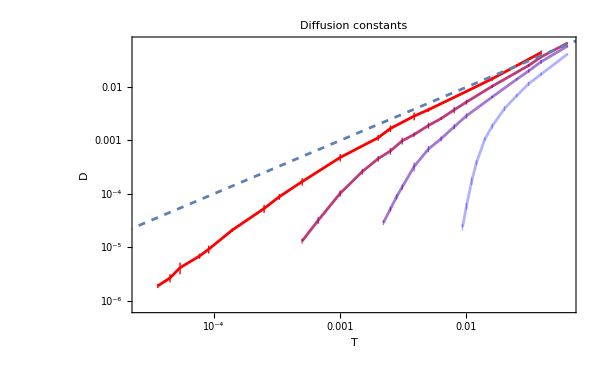

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],finalD[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],Joined->True,PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},ImageSize->600,PlotLabel->"Diffusion constants"],LogLogPlot[x,{x,0.00001,0.1},PlotStyle->Dashed]]
```

```mathematica
diffusionConstantTable=Table[Prepend[Table[{temperatures[[p,T]],meanD[[p,T]],stdD[[p,T]]},{T,Length[temperatures[[p]]]}],{"T","mean diffusion constants","std of diffusion constants"}],{p,Length[p0s]}]
```

{{{T,mean diffusion constants,std of diffusion constants},{0.039,0.0444514,0.0042275},{0.016,0.0143528,0.00125233},{0.01,0.00831702,0.000528286},{0.005,0.00376919,0.000335708},{0.00385,0.00286433,0.000482764},{0.0025,0.00167637,0.000236178},{0.002,0.00112627,0.000136571},{0.001,0.000480198,0.0000760202},{0.0005,0.000169223,0.0000264448},{0.00033,0.0000882432,0.0000106727},{0.00025,0.00005308,9.21629×10^-6},{0.00014,0.0000209377,1.51193×10^-6},{0.000091,9.13993×10^-6,1.5251×10^-6},{0.000077,6.81888×10^-6,7.64353×10^-7},{0.000054,4.12171×10^-6,1.02317×10^-6},{0.000045,2.65233×10^-6,4.64043×10^-7},{0.000036,1.87934×10^-6,1.69801×10^-7}},{{T,mean diffusion constants,std of diffusion constants},{0.063,0.0668539,0.0023196},{0.039,0.0368397,0.00186999},{0.03105,0.0254303,0.00160208},{0.016,0.0103878,0.000725366},{0.01,0.0052612,0.000560314},{0.008,0.0037525,0.000523673},{0.0063,0.00258202,0.000145315},{0.005,0.00190902,0.000243081},{0.00385,0.00129237,0.000119994},{0.0031,0.000986879,0.00014649},{0.0025,0.000634971,0.0000914617},{0.002,0.000456567,0.0000543455},{0.0015,0.000262289,0.0000324022},{0.001,0.000102172,0.0000136889},{0.00067,0.0000318861,4.48992×10^-6},{0.0005,0.0000130429,1.30584×10^-6}},{{T,mean diffusion constants,std of diffusion constants},{0.063,0.0586886,0.00284813},{0.039,0.0298947,0.00236446},{0.03105,0.0200875,0.00148802},{0.025,0.0140373,0.000722252},{0.016,0.0065418,0.000301741},{0.01,0.00289898,0.000338867},{0.008,0.001813,0.000193494},{0.0063,0.00107905,0.000110132},{0.005,0.000692833,0.0000928489},{0.00385,0.00032554,0.0000622705},{0.0031,0.000134316,0.0000152422},{0.0028,0.0000885356,0.0000100541},{0.0025,0.0000521229,5.60777×10^-6},{0.0022,0.0000287819,2.74087×10^-6}},{{T,mean diffusion constants,std of diffusion constants},{0.063,0.0416371,0.00128957},{0.039,0.0174648,0.00122647},{0.03105,0.0115399,0.00104096},{0.025,0.0069172,0.00051342},{0.02,0.00396559,0.000414943},{0.016,0.00186336,0.000201133},{0.014,0.00106872,0.0000712252},{0.012,0.000386935,0.0000370389},{0.011,0.000173611,0.0000271888},{0.01,0.0000590815,8.67768×10^-6},{0.0093,0.0000238246,3.23324×10^-6}}}

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>".csv",diffusionConstantTable[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.850.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.825.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.800.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.750.csv}

### CRMSD

```mathematica
CRdiffusionConstants=Table[Table[Table[trueCRMSDs[[p,T,i,2,Length[trueCRMSDs[[p,T,i,2]]]]]/4/(trueCRMSDs[[p,T,i,1,Length[trueCRMSDs[[p,T,i,1]]]]]-trueCRMSDs[[p,T,i,1,1]]),{i,10}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{0.0462782,0.0627178,0.0470894,0.0505109,0.0517328,0.0465428,0.051964,0.0476517,0.0494041,0.0506994},{0.0153225,0.0155036,0.0148723,0.0164444,0.0150932,0.014088,0.0176763,0.0148682,0.0148874,0.0143532},{0.00800326,0.00851078,0.00788051,0.00819398,0.00848643,0.00815655,0.00864262,0.00887828,0.00866627,0.00813074},{0.00327021,0.00344278,0.00318855,0.00332069,0.00364584,0.00323667,0.00344161,0.0034172,0.00341751,0.00335597},{0.00220455,0.00245447,0.00252191,0.00212826,0.00235464,0.00228172,0.00228295,0.00223261,0.00214199,0.00239966},{0.00124172,0.00127454,0.00121523,0.00121422,0.00122404,0.00120563,0.0012864,0.00124079,0.00126824,0.00120733},{0.000888648,0.000901008,0.000902884,0.000854252,0.000852659,0.000940576,0.000865142,0.000873203,0.000885534,0.000832482},{0.000271651,0.000282714,0.000279972,0.000272618,0.000267993,0.000263807,0.000274012,0.000268455,0.000266328,0.000274631},{0.0000744117,0.000076191,0.0000755873,0.0000774882,0.0000751502,0.0000775954,0.0000776017,0.0000749073,0.0000775342,0.0000785761},{0.0000358862,0.0000351777,0.0000371632,0.0000344018,0.0000392293,0.0000365964,0.0000357487,0.00003651,0.0000345922,0.0000355307},{0.0000411248,0.0000403221,0.0000409809,0.000042234,0.0000406398,0.0000417289,0.0000431234,0.000039581,0.0000428219,0.0000398794},{0.0000138336,0.0000127097,0.0000125556,0.0000127615,0.0000131663,0.0000126335,0.0000128028,0.0000126121,0.0000122165,0.0000127368},{5.05753×10^-6,4.89257×10^-6,5.26515×10^-6,5.02884×10^-6,5.07538×10^-6,5.15261×10^-6,5.10203×10^-6,4.88127×10^-6,5.06438×10^-6,4.91787×10^-6},{3.56043×10^-6,3.53675×10^-6,3.57844×10^-6,3.55536×10^-6,3.61486×10^-6,3.66321×10^-6,3.60329×10^-6,3.52756×10^-6,3.47443×10^-6,3.61223×10^-6},{1.72856×10^-6,1.68703×10^-6,1.7824×10^-6,1.7689×10^-6,1.64696×10^-6,1.82532×10^-6,1.6041×10^-6,1.71708×10^-6,1.68539×10^-6,1.68974×10^-6},{1.17797×10^-6,1.22163×10^-6,1.13876×10^-6,1.19453×10^-6,1.15511×10^-6,1.19651×10^-6,1.15828×10^-6,1.19277×10^-6,1.14332×10^-6,1.1923×10^-6},{7.91719×10^-7,7.85248×10^-7,7.55027×10^-7,7.78435×10^-7,7.80997×10^-7,7.70972×10^-7,7.61341×10^-7,7.92554×10^-7,7.73138×10^-7,7.5847×10^-7}},{{0.0760789,0.0829139,0.075414,0.0739852,0.0731362,0.0770217,0.0771988,0.0785694,0.0739309,0.0756678},{0.0431044,0.0399012,0.0378477,0.0406191,0.0425851,0.0401309,0.0454561,0.0416706,0.0416218,0.0403449},{0.0259785,0.0280932,0.0281785,0.0293217,0.0310487,0.0301921,0.0275229,0.0277082,0.0285783,0.0277599},{0.0103673,0.0115798,0.0103603,0.0107062,0.0100025,0.0104235,0.0115264,0.00995062,0.0104105,0.0106734},{0.00524451,0.00493474,0.00482703,0.00482398,0.00535243,0.0049639,0.00485406,0.0046213,0.00477526,0.00517702},{0.0033051,0.00359685,0.00353388,0.00358864,0.00333561,0.00322284,0.00315703,0.00339964,0.00316895,0.00330829},{0.00224344,0.00246736,0.00231455,0.00218174,0.00240291,0.0022964,0.00227467,0.00211286,0.00237462,0.00231536},{0.0015932,0.00144412,0.00158994,0.00152699,0.00153198,0.00151983,0.00160726,0.00160908,0.00141907,0.00156529},{0.00100687,0.000960699,0.00091077,0.000929722,0.00101003,0.0010013,0.000976375,0.000924811,0.000926741,0.000943909},{0.000614977,0.000652021,0.000603225,0.000632849,0.000669948,0.000602377,0.000635404,0.000599486,0.00066804,0.000630165},{0.000408859,0.000410337,0.000420967,0.000404185,0.000422929,0.000387993,0.000428377,0.000385605,0.000405718,0.000428304},{0.0002631,0.00025412,0.000267675,0.000263061,0.00025855,0.000260587,0.000242901,0.000262728,0.000254044,0.000249253},{0.000130202,0.000130653,0.000131841,0.000134309,0.000135922,0.000133055,0.000125142,0.000132576,0.000137819,0.000132417},{0.000098002,0.0000956132,0.0000867907,0.0000876443,0.0000892536,0.000100618,0.0000869015,0.0000946969,0.0000888438,0.0000880727},{0.0000256646,0.0000255762,0.000025444,0.0000212355,0.0000248129,0.0000225974,0.0000250185,0.0000250848,0.0000245688,0.0000254193},{7.83176×10^-6,7.48061×10^-6,8.43941×10^-6,8.3557×10^-6,7.7744×10^-6,7.91591×10^-6,7.62357×10^-6,7.87312×10^-6,7.53368×10^-6,7.0889×10^-6}},{{0.0669386,0.0676634,0.0684622,0.0640097,0.0626599,0.0695142,0.0644801,0.0715963,0.0641716,0.0692302},{0.0334654,0.036837,0.0319618,0.0314396,0.0348149,0.0340002,0.0307242,0.0300515,0.0299992,0.0312183},{0.0246285,0.0232757,0.0212478,0.0217745,0.0225757,0.0201958,0.0202338,0.0214617,0.0220576,0.0219083},{0.0143946,0.0150229,0.0153566,0.0144447,0.0145409,0.015715,0.014943,0.0141026,0.015722,0.0145741},{0.00642739,0.00646004,0.00644656,0.00664305,0.0061919,0.00636429,0.00640129,0.00631233,0.00650502,0.00670246},{0.00261802,0.0024676,0.00247931,0.00251489,0.00247305,0.00237352,0.00243693,0.00243399,0.00246183,0.0024538},{0.00143482,0.00147463,0.00145207,0.00155376,0.00143332,0.00156506,0.00143701,0.0014096,0.00153006,0.00148126},{0.000789997,0.000801408,0.000830293,0.00080626,0.000793381,0.000802579,0.000763832,0.000827933,0.000770384,0.000838638},{0.000425298,0.000415243,0.000419965,0.000435514,0.000425704,0.000415266,0.000401326,0.000429115,0.000423565,0.000425632},{0.000190215,0.000188691,0.000177993,0.000168699,0.00019046,0.000152777,0.000191873,0.000189735,0.000177097,0.000173571},{0.0000786994,0.0000787832,0.0000796508,0.000084758,0.000087673,0.0000893143,0.000082994,0.0000729621,0.0000838914,0.0000754903},{0.0000622759,0.0000640543,0.000063028,0.0000673447,0.0000641339,0.0000859383,0.0000891337,0.0000808891,0.0000849209,0.0000839355},{0.0000372033,0.0000371998,0.0000373756,0.0000360918,0.0000362638,0.0000368719,0.0000448634,0.0000474201,0.0000441025,0.0000442558},{0.0000215155,0.0000191645,0.0000152345,0.0000192986,0.0000262435,0.0000239929,0.0000232941,0.000021956,0.0000239174,0.0000236181}},{{0.0477437,0.0455329,0.0473882,0.0461155,0.0452294,0.047478,0.047725,0.0466096,0.048941,0.048015},{0.0173923,0.0178363,0.019954,0.0176504,0.0204424,0.0190475,0.0197068,0.0173309,0.0199399,0.0190945},{0.012342,0.0109254,0.011487,0.0121679,0.0114681,0.0120742,0.0115774,0.0110012,0.0119744,0.0110615},{0.00683368,0.00679054,0.00669485,0.00690936,0.00634295,0.00696629,0.00698331,0.00685685,0.00667438,0.00675338},{0.00344757,0.00349781,0.00337658,0.00381636,0.00381739,0.0035285,0.00360638,0.00359884,0.00345905,0.00327157},{0.00158443,0.00154224,0.00162574,0.00160044,0.00149301,0.00147419,0.00159916,0.00152412,0.00160903,0.00172563},{0.000868823,0.000873919,0.00084493,0.0008713,0.000849373,0.00089467,0.000888162,0.000917324,0.000834868,0.000868754},{0.000272872,0.000299666,0.000283037,0.000282383,0.000278649,0.000308437,0.000315159,0.000282779,0.00028598,0.000280058},{0.000122969,0.000134118,0.000127157,0.000157745,0.000120699,0.000137278,0.00014365,0.000119638,0.000115131,0.000129003},{0.000054739,0.0000433496,0.0000577852,0.0000576648,0.0000598241,0.0000499534,0.0000645291,0.0000492545,0.0000567188,0.0000504946},{0.0000249443,0.0000211377,0.0000229188,0.0000210034,0.0000219106,0.0000191248,0.0000214656,0.0000278968,0.0000251469,0.0000209672}}}

```mathematica
meanCRD=Table[Table[Mean[Table[CRdiffusionConstants[[p,T,i]],{i,10}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0504591,0.0153109,0.00835494,0.0033737,0.00230028,0.00123781,0.000879639,0.000272218,0.0000765043,0.0000360836,0.0000412436,0.0000128029,5.04376×10^-6,3.57266×10^-6,1.71355×10^-6,1.17712×10^-6,7.7479×10^-7},{0.0763917,0.0413282,0.0284382,0.0106,0.00495742,0.00336168,0.00229839,0.00154068,0.000959123,0.000630849,0.000410327,0.000257602,0.000132394,0.0000916437,0.0000245422,7.79171×10^-6},{0.0668726,0.0324512,0.0219359,0.0148816,0.00644543,0.00247129,0.00147716,0.00080247,0.000421663,0.000180111,0.0000814216,0.0000745654,0.0000401648,0.0000218235},{0.0470778,0.0188395,0.0116079,0.00678056,0.00354201,0.0015778,0.000871212,0.000288902,0.000130739,0.0000544313,0.0000226516}}

```mathematica
stdCRD=Table[Table[StandardDeviation[Table[CRdiffusionConstants[[p,T,i]],{i,10}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.00480033,0.00105119,0.000326504,0.000130872,0.000131134,0.0000295917,0.0000310448,5.93739×10^-6,1.43055×10^-6,1.40775×10^-6,1.20939×10^-6,4.31947×10^-7,1.20739×10^-7,5.36866×10^-8,6.58363×10^-8,2.70578×10^-8,1.34101×10^-8},{0.00283534,0.00208251,0.0014437,0.000557008,0.00023067,0.000164296,0.000104057,0.0000664276,0.000037432,0.0000262354,0.0000152465,7.5143×10^-6,3.44399×10^-6,5.10321×10^-6,1.46148×10^-6,4.00989×10^-7},{0.00292439,0.00225553,0.00133831,0.000567229,0.000148974,0.0000632773,0.0000547079,0.0000247357,9.39803×10^-6,0.000012682,5.22099×10^-6,0.000011216,4.40896×10^-6,3.1795×10^-6},{0.00117458,0.00118664,0.000513359,0.00018613,0.000175409,0.0000731892,0.0000246568,0.0000139448,0.0000128843,6.17552×10^-6,2.60994×10^-6}}

```mathematica
finalCRD=Table[Table[Around[meanCRD[[p,T]],stdCRD[[p,T]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0500.005,0.01530.0011,0.008350.00033,0.003370.00013,0.002300.00013,0.0012380.000030,0.0008800.000031,0.0002726,0.000076514,0.000036114,0.000041212,0.00001284,5.040.1210^-6,3.570.0510^-6,1.710.0710^-6,1.1770.02710^-6,7.750.1310^-7},{0.07640.0028,0.04130.0021,0.02840.0014,0.01060.0006,0.004960.00023,0.003360.00016,0.002300.00010,0.001540.00007,0.000960.00004,0.0006310.000026,0.0004100.000015,0.0002588,0.000132434,0.0000925,0.000024515,7.80.410^-6},{0.06690.0029,0.03250.0023,0.02190.0013,0.01490.0006,0.006450.00015,0.002470.00006,0.001480.00005,0.0008020.000025,0.0004229,0.0001800.000013,0.0000815,0.0000750.000011,0.0000404,0.000021832},{0.04710.0012,0.01880.0012,0.01160.0005,0.006780.00019,0.003540.00018,0.001580.00007,0.0008710.000025,0.0002890.000014,0.0001310.000013,0.0000546,0.000022726}}

```mathematica
finalCRD={{0.0500.005,0.01530.0011,0.008350.00033,0.003370.00013,0.002300.00013,0.0012380.000030,0.0008800.000031,0.0002726,0.000076514,0.000036114,0.000041212,0.00001284,5.040.1210^-6,3.570.0510^-6,1.710.0710^-6,1.1770.02710^-6,7.750.1310^-7},{0.07640.0028,0.04130.0021,0.02840.0014,0.01060.0006,0.004960.00023,0.003360.00016,0.002300.00010,0.001540.00007,0.000960.00004,0.0006310.000026,0.0004100.000015,0.0002588,0.000132434,0.0000925,0.000024515,7.80.410^-6},{0.06690.0029,0.03250.0023,0.02190.0013,0.01490.0006,0.006450.00015,0.002470.00006,0.001480.00005,0.0008020.000025,0.0004229,0.0001800.000013,0.0000815,0.0000750.000011,0.0000404,0.000021832},{0.04710.0012,0.01880.0012,0.01160.0005,0.006780.00019,0.003540.00018,0.001580.00007,0.0008710.000025,0.0002890.000014,0.0001310.000013,0.0000546,0.000022726}};
```

```mathematica
Export["/home/chengling/Research/updates/07282024/diffusion.jpeg",Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],finalD[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],Joined->True,PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},ImageSize->600,PlotLabel->"Diffusion constants",PlotLegends->Table["MSD p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],LogLogPlot[x,{x,0.00001,0.1},PlotStyle->Dashed],ListLogLogPlot[Table[Table[{temperatures[[p,T]],finalCRD[[p,T,1]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],Joined->True,PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},ImageSize->600,PlotLabel->"Diffusion constants",PlotMarkers->"OpenMarkers",PlotLegends->Table["CRMSD p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],LogLogPlot[x,{x,0.00001,0.1},PlotStyle->Dashed]]]
```

/home/chengling/Research/updates/07282024/diffusion.jpeg

```mathematica
CRdiffusionConstantTable=Table[Prepend[Table[{temperatures[[p,T]],meanCRD[[p,T]],stdCRD[[p,T]]},{T,Length[temperatures[[p]]]}],{"T","mean cage-relative diffusion constants","std of cage relative diffusion constants"}],{p,Length[p0s]}]
```

{{{T,mean cage-relative diffusion constants,std of cage relative diffusion constants},{0.039,0.0504591,0.00480033},{0.016,0.0153109,0.00105119},{0.01,0.00835494,0.000326504},{0.005,0.0033737,0.000130872},{0.00385,0.00230028,0.000131134},{0.0025,0.00123781,0.0000295917},{0.002,0.000879639,0.0000310448},{0.001,0.000272218,5.93739×10^-6},{0.0005,0.0000765043,1.43055×10^-6},{0.00033,0.0000360836,1.40775×10^-6},{0.00025,0.0000412436,1.20939×10^-6},{0.00014,0.0000128029,4.31947×10^-7},{0.000091,5.04376×10^-6,1.20739×10^-7},{0.000077,3.57266×10^-6,5.36866×10^-8},{0.000054,1.71355×10^-6,6.58363×10^-8},{0.000045,1.17712×10^-6,2.70578×10^-8},{0.000036,7.7479×10^-7,1.34101×10^-8}},{{T,mean cage-relative diffusion constants,std of cage relative diffusion constants},{0.063,0.0763917,0.00283534},{0.039,0.0413282,0.00208251},{0.03105,0.0284382,0.0014437},{0.016,0.0106,0.000557008},{0.01,0.00495742,0.00023067},{0.008,0.00336168,0.000164296},{0.0063,0.00229839,0.000104057},{0.005,0.00154068,0.0000664276},{0.00385,0.000959123,0.000037432},{0.0031,0.000630849,0.0000262354},{0.0025,0.000410327,0.0000152465},{0.002,0.000257602,7.5143×10^-6},{0.0015,0.000132394,3.44399×10^-6},{0.001,0.0000916437,5.10321×10^-6},{0.00067,0.0000245422,1.46148×10^-6},{0.0005,7.79171×10^-6,4.00989×10^-7}},{{T,mean cage-relative diffusion constants,std of cage relative diffusion constants},{0.063,0.0668726,0.00292439},{0.039,0.0324512,0.00225553},{0.03105,0.0219359,0.00133831},{0.025,0.0148816,0.000567229},{0.016,0.00644543,0.000148974},{0.01,0.00247129,0.0000632773},{0.008,0.00147716,0.0000547079},{0.0063,0.00080247,0.0000247357},{0.005,0.000421663,9.39803×10^-6},{0.00385,0.000180111,0.000012682},{0.0031,0.0000814216,5.22099×10^-6},{0.0028,0.0000745654,0.000011216},{0.0025,0.0000401648,4.40896×10^-6},{0.0022,0.0000218235,3.1795×10^-6}},{{T,mean cage-relative diffusion constants,std of cage relative diffusion constants},{0.063,0.0470778,0.00117458},{0.039,0.0188395,0.00118664},{0.03105,0.0116079,0.000513359},{0.025,0.00678056,0.00018613},{0.02,0.00354201,0.000175409},{0.016,0.0015778,0.0000731892},{0.014,0.000871212,0.0000246568},{0.012,0.000288902,0.0000139448},{0.011,0.000130739,0.0000128843},{0.01,0.0000544313,6.17552×10^-6},{0.0093,0.0000226516,2.60994×10^-6}}}

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/cageRelativeDiffudionConstantTableP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>".csv",CRdiffusionConstantTable[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/cageRelativeDiffudionConstantTableP3.850.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/cageRelativeDiffudionConstantTableP3.825.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/cageRelativeDiffudionConstantTableP3.800.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/cageRelativeDiffudionConstantTableP3.750.csv}